```mathematica
A[y_,t_,px_]:=√(y^2/4-px/t*(y-1)^2);
u[y_,t_,px_]:=-y/(4*px*(A[y,t,px])^2)+(1-y)^2/(8*t*(A[y,t,px])^3)*Log[(y/2+A[y,t,px])^2/(y/2-A[y,t,px])^2]+y/(8*px*A[y,t,px])*Log[(y/2+A[y,t,px])^2/(y/2-A[y,t,px])^2];
v[y_,t_,px_] :=(1-y)^2/(8*t*(A[y,t,px])^3)* Log[(y/2+A[y,t,px])^2/(y/2-A[y,t,px])^2];
g[y_,t_,px_] := y/(8*px*A[y,t,px])*Log[(y/2+A[y,t,px])^2/(y/2-A[y,t,px])^2];
h[y_,t_,px_] := -y/(4*px*(A[y,t,px])^2);
exp:=10^-33;
Table[NIntegrate[u[y,t+I*exp,px-I*exp],{y,0,0.9999999}],{t,-4,-1},{px,1,4}]//MatrixForm
```

(-1.68112×10^-6-1.71862×10^-39 ⅈ | -8.23233×10^-7-4.17867×10^-40 ⅈ | -5.42065×10^-7-1.82077×10^-40 ⅈ | -4.02952×10^-7-1.00738×10^-40 ⅈ
-1.66674×10^-6-1.70007×10^-39 ⅈ | -8.16041×10^-7-4.12187×10^-40 ⅈ | -5.3727×10^-7-1.7909×10^-40 ⅈ | -3.99356×10^-7-9.87974×10^-41 ⅈ
-1.64647×10^-6-1.67147×10^-39 ⅈ | -8.05905×10^-7-4.02952×10^-40 ⅈ | -5.30512×10^-7-1.7406×10^-40 ⅈ | -3.94288×10^-7-9.5447×10^-41 ⅈ
-1.61181×10^-6-1.61181×10^-39 ⅈ | -7.88576×10^-7-3.81788×10^-40 ⅈ | -5.1896×10^-7-1.61875×10^-40 ⅈ | -3.85624×10^-7-8.70309×10^-41 ⅈ)

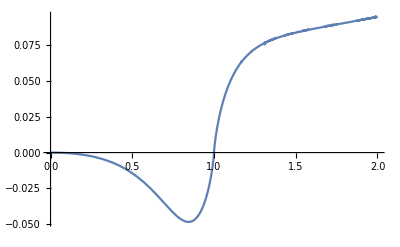

```mathematica
Plot[Re[NIntegrate[u[y,-2+I*exp,4-I*exp],{y,0,x}]],{x,0,2}]
```

```mathematica
Table[NIntegrate[u[y,t,px],{y,0,0.9999999}],{t,-4,-1},{px,1,4}]//MatrixForm
```

(-1.68112×10^-6 | -8.23233×10^-7 | -5.42065×10^-7 | -4.02952×10^-7
-1.66674×10^-6 | -8.16041×10^-7 | -5.3727×10^-7 | -3.99356×10^-7
-1.64647×10^-6 | -8.05905×10^-7 | -5.30512×10^-7 | -3.94288×10^-7
-1.61181×10^-6 | -7.88576×10^-7 | -5.1896×10^-7 | -3.85624×10^-7)

```mathematica
Plot[NIntegrate[u[y,-2,4],{y,0,x}],{x,0,2}]
```

-Graphics-

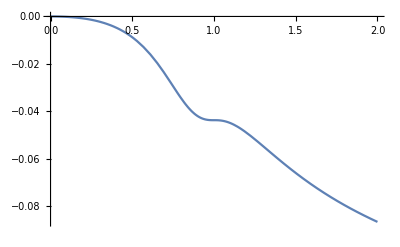

```mathematica
Plot[Re[NIntegrate[v[y,-2+I*exp,4-I*exp],{y,0,x}]],{x,0,2}]
```

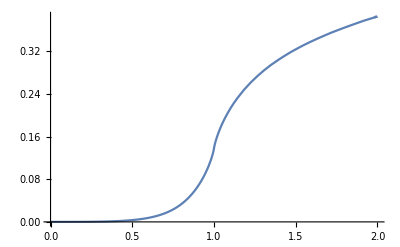

```mathematica
Plot[Re[NIntegrate[g[y,-2+I*exp,4-I*exp],{y,0,x}]],{x,0,2}]
```

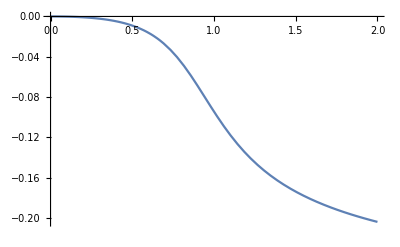

```mathematica
Plot[Re[NIntegrate[h[y,-2+I*exp,4-I*exp],{y,0,x}]],{x,0,2}]
```

```mathematica
Integrate[u[y,-2+I*exp,5-I*exp],{y,0,1}]
```

0